#### gr. 1

Zad. 1

-24 x-6 x^2+8 x^3+3 x^4

-24-12 x+24 x^2+12 x^3

{{x→-2},{x→-1},{x→1}}

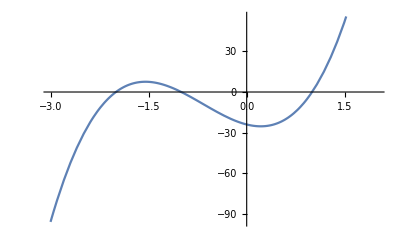

```mathematica
(x-1)(x+1)(x+2)//Expand;
12Integrate[%,x]//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-3,2}]
```

Zad. 2

```mathematica
(* (a) *)
```

```mathematica
L=Exp[2x]-1//Expand;
M=Sin[3x]//Expand;
L/M;
Limit[L/M,x->0]
(* (b)  calka od 0 do 2 *)
f[x_]:=x^2;
a1=f[0];
b1=f[1/2];
c1=f[1];
ml=f[0]/2+f[1/2]/2
mr=f[1/2]/2+f[1]/2
```

2/3

1/8

5/8

Zad. 3

```mathematica
Integrate[x^3-1/x^3,x]
Integrate[1/Sqrt[2-3x],x]
Integrate[x^2 Log[x],x]
```

1/(2 x^2)+x^4/4

-2/3 √(2-3 x)

-x^3/9+1/3 x^3 Log[x]

#### gr. 2

Zad. 1

4-4 x-x^2+x^3

48 x-24 x^2-4 x^3+3 x^4

48-48 x-12 x^2+12 x^3

{{x→-2},{x→1},{x→2}}

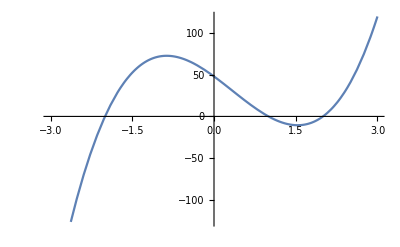

```mathematica
(x-2)(x+2)(x-1)//Expand
12Integrate[%,x]//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-3,3}]
```

Zad. 2

```mathematica
(* (a) *)
```

```mathematica
L=Expand[(x-2)(x+3)];
M=Expand[(x+3)(2x+1)^2];
Limit[L/M,x->-3]
(* (b) *)
f[x_]:=x^2;
a1=f[2];
b1=f[5/2];
c1=f[3];
mL=(f[2]+f[5/2])/2
mR=(f[5/2]+f[3])/2
```

-1/5

41/8

61/8

Zad. 3

```mathematica
Integrate[10/(x^2+1)-2/((x^5)^(1/3)),x]
Integrate[Cos[x^2]x,x]
Integrate[x Exp[3x],x]
```

(3 x)/((x^5)^(1/3))+10 ArcTan[x]

Sin[x^2]/2

ⅇ^(3 x) (-1/9+x/3)